The International Interaction Game

Finding the Probability of Two Counties Engaging into War

We will consider uniquely the subgame crisis where we only have Force (F) or Not Force (F̃) as actions.

Pr(War_B , War_A) = (F_B F_A OverTilde[F_B]|S⟩ + F_A F_B|S⟩ |)^2

```mathematica
(* defining the superposition state S according to B's basis*)
```

```mathematica
SB= ({{1}, {1}})* 1/(√2);
```

```mathematica
MatrixForm[SB]
```

(1/(√2)
1/(√2))

```mathematica
(* Define the Projector Operator ~F1B and F1B and basis FB *)
```

```mathematica
Subscript[F1, B̄]=({{0, 0}, {0, 1}}); Subscript[F1, B]=({{1, 0}, {0, 0}});Subscript[F, B]=({{1, 0}, {0, 1}});
```

```mathematica
(* status quo as being cooperative *)
```

```mathematica
(* Define the Rotation Operator for Player A using Force *)
```

```mathematica
R = ({{Cos[Re[ϕ]], -Sin [Re[ϕ]]}, {Sin [Re[ϕ]], Cos [Re[ϕ]]}});
```

```mathematica
Subscript[F1, A]=R.({{1}, {0}});
```

```mathematica
MatrixForm[Subscript[F1, A]]
```

(Cos[Re[ϕ]]
Sin[Re[ϕ]])

```mathematica
(* Define the Rotation Operator for Player B  *)
```

```mathematica
R2 = ({{Cos[Re[θ]], -Sin [Re[θ]]}, {Sin [Re[θ]], Cos [Re[θ]]}});
```

```mathematica
(* Rotating from player A's basis back to player B's basis*)
```

```mathematica
Subscript[F1, RAtoB]=FullSimplify[Inverse[Subscript[F, B]]. R2. Subscript[F, B] . Subscript[F1, A] ]
```

{{Cos[Re[θ+ϕ]]},{Sin[Re[θ+ϕ]]}}

```mathematica
(* Rotating from player B's basis to a new Basis where B attacks *)
```

```mathematica
Rfb =FullSimplify[ ({{0, 1}, {1, 0}}) . Subscript[F1, RAtoB] ]
```

{{Sin[Re[θ+ϕ]]},{Cos[Re[θ+ϕ]]}}

```mathematica
fb = Rfb({{1}, {0}})
```

{{Sin[Re[θ+ϕ]]},{0}}

```mathematica
Subscript[F1, B̄] . SB
```

{{0},{1/(√2)}}

```mathematica
(* Probability of war given that B started *)
```

```mathematica
probBwarAwar = FullSimplify[Norm[fb Subscript[F1, RAtoB] Subscript[F1, B̄] . SB + Subscript[F1, RAtoB] Subscript[F1, B] . SB]^2]
```

1/2 Cos[Re[θ+ϕ]]^2

```mathematica
(* PROBLEM: the projection model means that when B does not make a move, then there is no possibility that B can make a move after A *)
```

```mathematica
MatrixForm[fb Subscript[F1, RAtoB] Subscript[F1, B̄].SB]
```

(0
0)

```mathematica
Plot3D[probBwarAwar,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},ColorFunction->(ColorData["DarkRainbow"][#3]&)]
```

-Graphics3D-

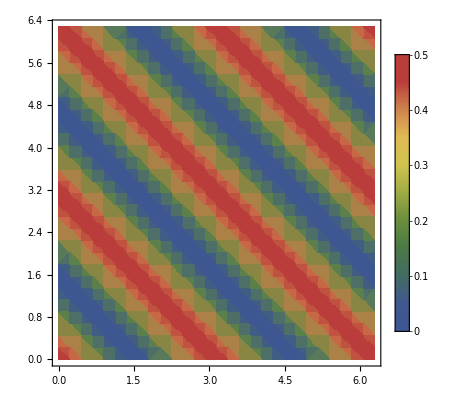

```mathematica
DensityPlot[probBwarAwar, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

Computing Probabilities when A starts

```mathematica
(* We need to define the superposition state according to A's basis *)
```

```mathematica
SA = FullSimplify[Inverse[R].({{0, 1}, {1, 0}}).R. SB];
```

```mathematica
MatrixForm[SA]
```

((Cos[2 Re[ϕ]]+Sin[2 Re[ϕ]])/(√2)
(Cos[2 Re[ϕ]]-Sin[2 Re[ϕ]])/(√2))

```mathematica
Subscript[F2, A]=({{Cos[Re[ϕ]]}, {Sin[Re[ϕ]]}}); Subscript[F2, Ā]=({{-Sin[Re[ϕ]]}, {Cos[Re[ϕ]]}}); (* basis of A *)
```

```mathematica
Norm[Subscript[F2, A]]^2
```

Cos[Re[ϕ]]^2+Sin[Re[ϕ]]^2

```mathematica
(* Then, we define Player's B roation according to A *)
```

```mathematica
Subscript[F2, B]=R2 .({{1}, {0}})
```

{{Cos[Re[θ]]},{Sin[Re[θ]]}}

```mathematica
MatrixForm[Subscript[F2, A] Subscript[F2, B] Subscript[F2, Ā] SA ]
```

(-(Cos[Re[θ]] Cos[Re[ϕ]] Sin[Re[ϕ]] (Cos[2 Re[ϕ]]+Sin[2 Re[ϕ]]))/(√2)
(Cos[Re[ϕ]] Sin[Re[θ]] Sin[Re[ϕ]] (Cos[2 Re[ϕ]]-Sin[2 Re[ϕ]]))/(√2))

```mathematica
probAwarBwar =  FullSimplify[Norm[Subscript[F2, A] Subscript[F2, B] Subscript[F2, Ā] SA +Subscript[F2, B] Subscript[F2, A] SA]^2]
```

1/2 (-(1+Cos[Re[ϕ]])^2 Sin[Re[θ]]^2 Sin[Re[ϕ]]^2 (-1+Sin[4 Re[ϕ]])+Cos[Re[θ]]^2 Cos[Re[ϕ]]^2 (-1+Sin[Re[ϕ]])^2 (1+Sin[4 Re[ϕ]]))

```mathematica
Plot3D[probAwarBwar,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},ColorFunction->(ColorData["DarkRainbow"][#3]&)]
```

-Graphics3D-

Final Probability of WAR: Pr(WarB, WarA) + Pr(WarA, WarB)

```mathematica
final = FullSimplify[(probBwarAwar + probAwarBwar)/2]
```

1/4 (Cos[Re[θ+ϕ]]^2-(1+Cos[Re[ϕ]])^2 Sin[Re[θ]]^2 Sin[Re[ϕ]]^2 (-1+Sin[4 Re[ϕ]])+Cos[Re[θ]]^2 Cos[Re[ϕ]]^2 (-1+Sin[Re[ϕ]])^2 (1+Sin[4 Re[ϕ]]))

```mathematica
Plot3D[final,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},ColorFunction->(ColorData["DarkRainbow"][#3]&)]
```

-Graphics3D-

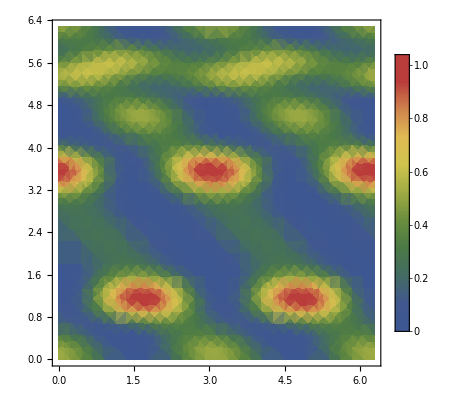

```mathematica
DensityPlot[final, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

```mathematica
(* TODO: Capitulation and Negotiation *)
```

```mathematica
(* look at big countries +- 3 countries *)
```

```mathematica
(* do the same on country level and try to interpret the differences between them *)
```